```mathematica
(*一个解微分方程的例子:《计算物理基础_彭芳麟》 Page347 求解温度场*)
eqn = D[u[x,y],{x,2}] + D[u[x,y],{y,2}] == 0;
```

```mathematica
c1 = u[0,y]==0;
c2 = u[100,y]==10;
c3 = u[x,0] == 0;
c4 = u[x,100] == 0;
```

```mathematica
s = NDSolve[{eqn,c1,c2,c3,c4},u,{x,0,100},{y,0,100}]
```

{{u→InterpolatingFunction[{{0., 100.}, {0., 100.}}, <>]}}

```mathematica
Plot3D[Evaluate[u[x,y]/.%],{x,0,100},{y,0,100},PlotRange->All]
```

-Graphics3D-

```mathematica
(*二维偕振子: 不加微扰的情况*)
a = 0.5;
ode1 = {x''[t] == -2*a*x[t],x[0]==0,x'[0]==1};
xsol = NDSolve[ode1,x, {t,0,20}];
```

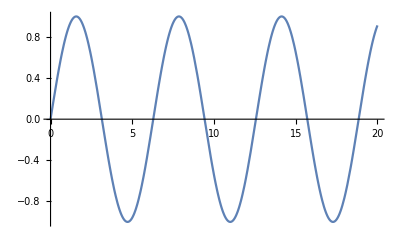

```mathematica
Plot[x[t]/.xsol,{t,0,20}]
```

```mathematica
ode2 = {y''[t] == -2*a*y[t],y[0]==1,y'[0]==0};
ysol = NDSolve[ode2,y,{t,0,20}];
```

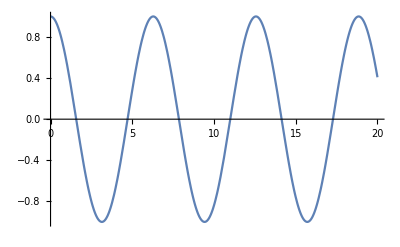

```mathematica
Plot[y[t]/.ysol,{t,0,20}]
```

```mathematica
Animate[Graphics[{Circle[],PointSize[Large],Pink,Point[{First[x[t]/.xsol],First[y[t]/.ysol]}]}],{t,0,20},AnimationRunning-> False]
```

```mathematica
(*添加微扰*)
e1 = 0.1;
e2 = 0;
ode3 = {x''[t] == -2*a*x[t] -3*e1*(x[t])^2,x[0]==0,x'[0]==1};
xsol2= NDSolve[ode3,x, {t,0,100}];
ode4 = {y''[t] == -2*a*y[t] -3*e2*(y[t])^2,y[0]==1,y'[0]==0};
ysol2= NDSolve[ode4,y, {t,0,100}];
Animate[Graphics[{LightGray,Point[{0,0}],Point[{-2,-2}],Point[{-2,2}],Point[{2,2}],Point[{2,-2}],Circle[{0,0},1],PointSize[Large],Pink,Point[{First[x[t]/.xsol2],First[y[t]/.ysol2]}]},AspectRatio->1,Axes->True],{t,0,100},AnimationRate->1,RefreshRate->60,DisplayAllSteps->True,AnimationRunning-> True]
```

```mathematica
e1 = 0.05;
e2 = -0.1;
sol = Quiet@NDSolve[{x''[t] == -2*a*x[t] -3*e1*(x[t])^2,x[0]==0,x'[0]==1,y''[t] == -2*a*y[t] -3*e2*(y[t])^2,y[0]==1,y'[0]==0},{x[t],y[t]},{t,0,100}];
dat=Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol,{t,0,tt},PlotRange->2,AxesLabel->{x[t],y[t]}]],{tt,.1,100,.2}];
SetDirectory@NotebookDirectory[]
ListAnimate[dat]
Export["home_3.gif",dat]
```

/home/jack/Documents/Wolfram Mathematica

home_3.gif

```mathematica
a = 0.5;
{"e1",Slider[Dynamic[e1],{-0.1,0.1,0.01}],Dynamic[e1]}
{"e2",Slider[Dynamic[e2],{-0.1,0.1,0.01}],Dynamic[e2]}
{"e3",Slider[Dynamic[e3],{-0.1,0.1,0.01}],Dynamic[e3]}
```

{e1,,}

{e2,,}

{e3,,}

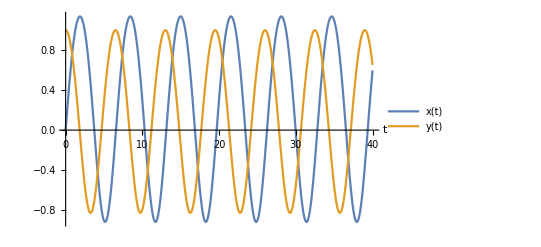

```mathematica
sol =Quiet@NDSolve[{x''[t] == -(2*a*x[t] +3*e1*(x[t])^2 +3*e3*(x[t])^2*(y[t])^3),x[0]==0,x'[0]==1,y''[t] == -(2*a*y[t] +3*e2*(y[t])^2 +3*e3*(x[t])^3*(y[t])^2),y[0]==1,y'[0]==0},{x[t],y[t]},{t,0,250}];

Plot[{x[t]/.sol, y[t]/.sol}, {t,0,40}, PlotLegends->{"x(t)","y(t)"},AxesLabel->Automatic]

dat=Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol,{t,0,tt},PlotRange->2,AxesLabel->{x[t],y[t]}]],{tt,.1,250,.2}];
ListAnimate[dat]
```

```mathematica
SetDirectory@NotebookDirectory[];
Export["home_e1_m0.1_e2_m0.1_e3_m0.gif",dat]
```

home_e1_m0.1_e2_m0.1_e3_m0.gif

```mathematica
Export["home_answer_e1_m0.1_e2_m0.1_e3_m0.svg",output1]
```

home_answer_e1_m0_e2_m0_e3_m0.svg